```mathematica
SetOptions[ EvaluationNotebook[], WindowSize -> Small ]
```

### Load packages

```mathematica
<<NFPackages`structuralMechanicsBook` // Quiet;
```

### Examples

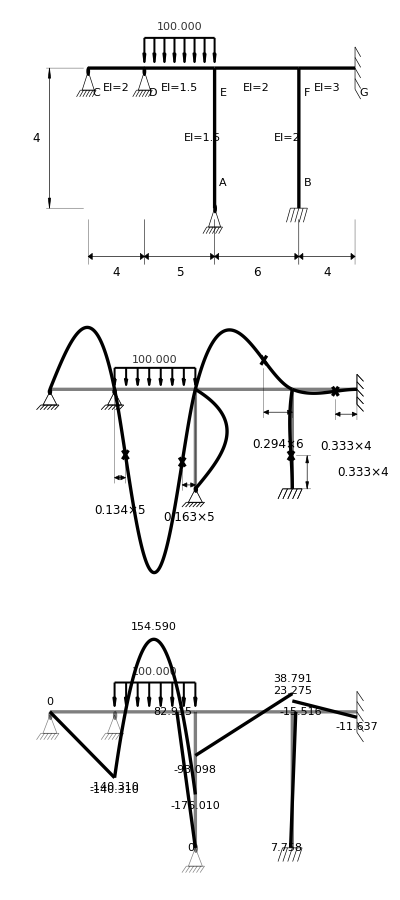

```mathematica
makeBuildingVerticalSpecsAndSolutionGrid[ {4}, {4, 5, 6, 4},600,
buildingBeamUniformLoadList -> { {1, 2} -> 100},
buildingBeamPointForceList -> { },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {{1, 1} -> 2, {1, 2} -> 1.5, {1, 3} -> 2, {1, 4}-> 3},
buildingColumnsEIMagnitudeList -> {{1, 3} -> 1.5, {1, 4}-> 2, _ -> 1},
buildingColumnOmitList -> { {1, 1} -> True, {1, 2} -> True, {1, 3} -> False, {1, 4}-> False, {1, 5} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {},
buildingSideSupportRightList -> { _ -> "fixed"},
buildingSupportList -> {1 -> "hinge", 2 -> "hinge", 3 -> "hinge", 4 -> "fixed", 5 -> "hinge"},
buildingFactorDisplacement->4 Automatic,
buildingFactorMomentDiagrams -> 0.002,
buildingSolveColumnBeamDisplacementFunctions -> False ]
```

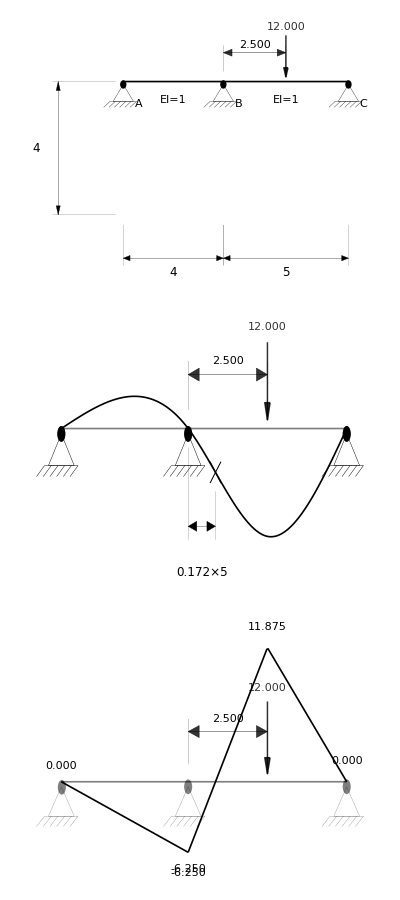

```mathematica
makeBuildingVerticalSpecsAndSolutionGrid[ {4}, {4, 5},300,
buildingBeamUniformLoadList -> { },
buildingBeamPointForceList -> { {1, 2} -> {0.5, 12} },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { {1, 1} -> True, {1, 2} -> True, {1, 3} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {},
buildingSideSupportRightList -> { _ -> None},
buildingSupportList -> {1 -> "hinge", 2 -> "hinge"},
buildingFactorMomentDiagrams -> 0.03,
buildingSolveColumnBeamDisplacementFunctions -> False ]
```

```mathematica
makeBuildingVerticalLoaded[ {4}, {4, 5},
buildingBeamUniformLoadList -> { },
buildingBeamPointForceList -> { {1, 2} -> {0.5, 12} },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { {1, 1} -> True, {1, 2} -> True, {1, 3} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {},
buildingSideSupportRightList -> {1 -> "hinge", _ -> None},
buildingSupportList -> {1 -> "hinge", 2 -> "hinge"},
buildingFactorMomentDiagrams -> 0.03,
buildingSolveColumnBeamDisplacementFunctions -> True ]
```

{dimensionalColumnDispFct$2021,dimensionalBeamDispFct$2021}

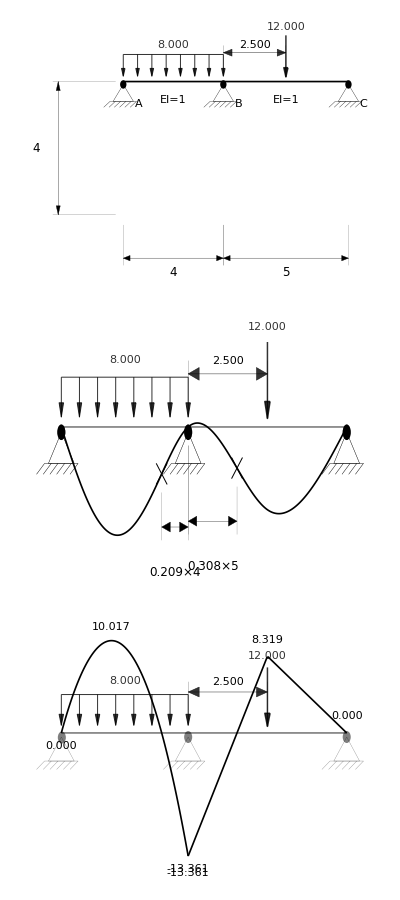

```mathematica
makeBuildingVerticalSpecsAndSolutionGrid[ {4}, {4, 5},300,
buildingBeamUniformLoadList -> { {1, 1} -> 8},
buildingBeamPointForceList -> { {1, 2} -> {0.5, 12} },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { {1, 1} -> True, {1, 2} -> True, {1, 3} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {},
buildingSideSupportRightList -> { _ -> None},
buildingSupportList -> {1 -> "hinge", 2 -> "hinge"},
buildingFactorMomentDiagrams -> 0.03,
buildingSolveColumnBeamDisplacementFunctions -> False ]
```

```mathematica
Manipulate[
makeBuildingVerticalSpecsAndSolutionGrid[ {4}, {4, 4, 4},300,
buildingBeamUniformLoadList -> { If[ uni, {1, 1} -> 2^log2w, {2, 1} -> 0] },
buildingBeamPointForceList -> { If[ poi, {1, whichMember} -> {dF, 2^log2P}, {2, whichMember} -> {dF, 0}] },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { {1, 1} -> True, {1, 2} -> True, {1, 3 | 4} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {},
buildingSideSupportRightList -> { _ -> None},
buildingSupportList -> {1 -> "hinge", 2 -> "hinge", 3 -> "hinge", 4 -> "hinge"},
buildingFactorMomentDiagrams -> 0.1mfac,
buildingSolveColumnBeamDisplacementFunctions -> False ],
{{log2w, 3, Dynamic[ Row[ {"w = " , 2^log2w}]]}, -3, 7, 1},
{{log2P, 3, Dynamic[ Row[ {"P = " , 2^log2P}]]}, -3, 7, 1}, 
{{dF, 0.5, Dynamic[ Row[ {"dF = " , dF * 4}]]}, 0.05, 0.95, 0.05}, 
{{whichMember, 3}, {2, 3}},
{{uni, True}, {True,False}},
{{poi, True}, {True, False}},
{{mfac, 0.5}, {0.02,0.05, 0.1, 0.25, 0.5, 1}, ControlType -> SetterBar},
ControlPlacement -> Left
]
```

```mathematica
SetOptions[ EvaluationNotebook[], Magnification -> 1.65 ]
```

### More examples

#### Ex 1

```mathematica
Manipulate[
makeBuildingVerticalSpecsAndSolutionGrid[ {4}, {4, 4, 4},300,
buildingBeamUniformLoadList -> { If[ uni, {1, 1} ->(10/8) 2^log2w, {2, 1} -> 0] },
buildingBeamPointForceList -> { If[ poi, {1, whichMember} -> {0.5,(10/8) 2^log2P}, {2, whichMember} -> {0.5, 0}] },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { {1, 1} -> True, {1, 2} -> True, {1, 3 | 4 | 5} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {1 -> None},
buildingSideSupportRightList -> {1 -> None },
buildingSupportList -> {1 -> "hinge", 2 -> "hinge", 3 -> "hinge", 4 -> "hinge"},
buildingFactorMomentDiagrams -> 0.1mfac,
buildingSolveColumnBeamDisplacementFunctions -> False ],
{{log2w, 3, Dynamic[ Row[ {"w = " ,(10/8) 2^log2w}]]}, -3, 7, 1},
{{log2P, 3, Dynamic[ Row[ {"P = " ,(10/8) 2^log2P}]]}, -3, 7, 1}, 
{{whichMember, 3}, {2, 3}},
{{uni, True}, {True,False}},
{{poi, True}, {True, False}},
{{mfac, 0.5}, {0.02,0.05, 0.1, 0.25, 0.5, 1}, ControlType -> SetterBar},
ControlPlacement -> Left
]
```

#### Ex 2

```mathematica
Manipulate[
makeBuildingVerticalSpecsAndSolutionGrid[ {4}, {4, 4, 4, 4},300,
buildingBeamUniformLoadList -> { If[ uni, {1, 1} -> 2^log2w, {2, 1} -> 0] },
buildingBeamPointForceList -> { If[ poi, {1, whichMember} -> {0.5, 2^log2P}, {2, whichMember} -> {0.5, 0}] },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { {1, 1} -> True, {1, 2} -> If[ noColumnOn2, True, False ], {1, 3 | 4 | 5} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> { If[ leftFixed, 1 ->"fixed", _ -> None ]},
buildingSideSupportRightList -> {If[ rightFixed, 1 ->"fixed", _ -> None ], _ -> None},
buildingSupportList -> {1 -> "hinge", 2 -> If[ noColumnOn2, "hinge", "fixed" ], 3 -> "hinge", 4 -> "hinge"},
buildingFactorMomentDiagrams -> 0.1mfac,
buildingSolveColumnBeamDisplacementFunctions -> False ],
{{log2w, 3, Dynamic[ Row[ {"w = " , 2^log2w}]]}, -3, 7, 1},
{{log2P, 3, Dynamic[ Row[ {"P = " , 2^log2P}]]}, -3, 7, 1}, 
{{whichMember, 3}, {2, 3, 4}},
{{uni, True}, {True,False}},
{{poi, True}, {True, False}},
{{mfac, 0.5}, {0.02,0.05, 0.1, 0.25, 0.5, 1}, ControlType -> SetterBar},
{{leftFixed, False}, {False, True}},
{{rightFixed, False}, {False, True}},
{{noColumnOn2, True}, {False, True}},
ControlPlacement -> Left
]
```

#### Ex 3

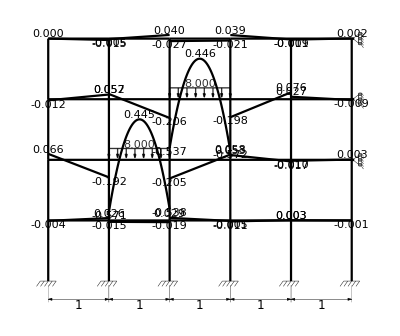

```mathematica
makeBuildingVerticalLoaded[ {1, 1, 1, 1 }, {1, 1, 1, 1, 1},
buildingBeamUniformLoadList -> { {3, 3} ->  8 ,  {2, 2} -> 8 },
buildingBeamPointForceList -> {  },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { },
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {1 -> None},
buildingSideSupportRightList -> {1 -> None },
buildingSupportList -> {1 -> "fixed", 2 -> "fixed", 3 -> "fixed", 4 -> "fixed"},
buildingSolveColumnBeamDisplacementFunctions -> False,

buildingDimensionLabelHeightList -> None,
buildingFactorMomentDiagrams -> 1,
buildingShowBeamMoments -> True,
buildingFactorDisplacement -> 10,
buildingShowUndeformedDeformedList -> {True, False}
] // Graphics
```

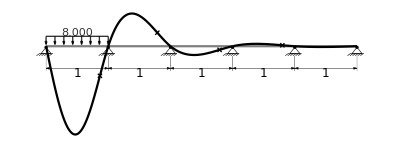

```mathematica
makeBuildingVerticalLoaded[ {0.1}, {1, 1, 1, 1, 1},
buildingBeamUniformLoadList -> { {1, 1} ->  8 },
buildingBeamPointForceList -> {  },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { {1, _} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {1 -> None},
buildingSideSupportRightList -> {1 -> None },
buildingSupportList -> {1 -> "hinge", 2 -> "hinge", 3 -> "hinge", 4 -> "hinge"},
buildingSolveColumnBeamDisplacementFunctions -> False,

buildingDimensionLabelHeightList -> None,
buildingFactorMomentDiagrams -> 1,
buildingShowBeamMoments -> False,
buildingFactorDisplacement -> 20,
buildingShowUndeformedDeformedList -> {True, True}
] // Graphics
```

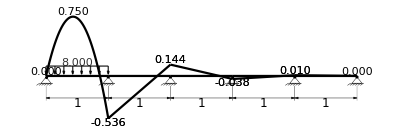

```mathematica
makeBuildingVerticalLoaded[ {0.1}, {1, 1, 1, 1, 1},
buildingBeamUniformLoadList -> { {1, 1} ->  8 },
buildingBeamPointForceList -> {  },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { {1, _} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {1 -> None},
buildingSideSupportRightList -> {1 -> None },
buildingSupportList -> {1 -> "hinge", 2 -> "hinge", 3 -> "hinge", 4 -> "hinge"},
buildingFactorMomentDiagrams -> 1,
buildingSolveColumnBeamDisplacementFunctions -> False,

buildingDimensionLabelHeightList -> None,
buildingShowBeamMoments -> True,
buildingShowUndeformedDeformedList -> {True, False}
] // Graphics
```

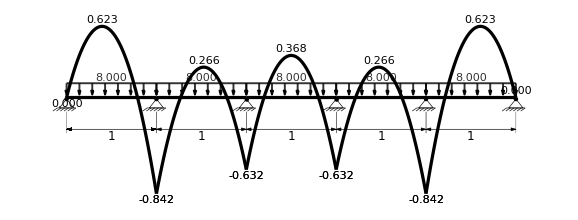

```mathematica
makeBuildingVerticalLoaded[ {0.1}, {1, 1, 1, 1, 1},
buildingBeamUniformLoadList -> { {1, _} ->  8 },
buildingBeamPointForceList -> {  },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { {1, _} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {1 -> None},
buildingSideSupportRightList -> {1 -> None },
buildingSupportList -> {1 -> "hinge", 2 -> "hinge", 3 -> "hinge", 4 -> "hinge"},
buildingFactorMomentDiagrams -> 1,
buildingSolveColumnBeamDisplacementFunctions -> False,

buildingDimensionLabelHeightList -> None,
buildingShowBeamMoments -> True,
buildingShowUndeformedDeformedList -> {True, False}
] // Graphics
```

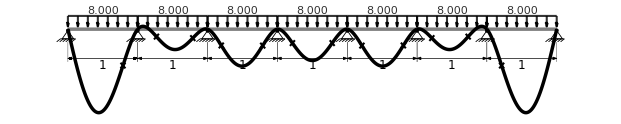

```mathematica
makeBuildingVerticalLoaded[ {0.1}, {1, 1, 1, 1, 1, 1, 1},
buildingBeamUniformLoadList -> { {1, _} ->  8 },
buildingBeamPointForceList -> {  },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { {1, _} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {1 -> None},
buildingSideSupportRightList -> {1 -> None },
buildingSupportList -> {1 -> "hinge", 2 -> "hinge", 3 -> "hinge", 4 -> "hinge"},
buildingFactorMomentDiagrams -> 1,
buildingSolveColumnBeamDisplacementFunctions -> False,

buildingFactorDisplacement -> 20,
buildingDimensionLabelHeightList -> None,
buildingShowBeamMoments -> False,
buildingShowUndeformedDeformedList -> {True, True}
] // Graphics
```

#### Ex 4

```mathematica
Manipulate[
makeBuildingVerticalSpecsAndSolutionGrid[ {4}, {4, 4, 4, 4, 4, 4},700,
buildingBeamUniformLoadList -> { {1, 1} ->(10/8) },
buildingBeamPointForceList -> {  },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { {1, 1} -> True, {1, 2} -> True, {1, _} -> True},
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {1 -> None},
buildingSideSupportRightList -> {1 -> None },
buildingSupportList -> {1 -> "hinge", 2 -> "hinge", 3 -> "hinge", 4 -> "hinge"},
buildingFactorMomentDiagrams -> 0.1mfac,
buildingSolveColumnBeamDisplacementFunctions -> False ],
{{mfac, 0.5}, {  1, 4, 8}, ControlType -> SetterBar},
ControlPlacement -> Left
]
```

### Combined loading

#### Spans ‘far’

```mathematica
Row[ Table[Graphics[ makeBuildingVerticalLoaded[ {3, 3,3   }, {5, 5,5  },
buildingBeamUniformLoadList -> wn,
buildingBeamPointForceList -> {  },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { },
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {1 -> None},
buildingSideSupportRightList -> {1 -> None },
buildingSupportList -> {1 -> "fixed", 2 -> "fixed", 3 -> "fixed", 4 -> "fixed"},
buildingSolveColumnBeamDisplacementFunctions -> False,

buildingDimensionLabelHeightList -> None,
buildingShowBeamMoments -> True,
buildingFactorDisplacement -> 0.01,
buildingFactorMomentDiagrams -> 0.03,
buildingShowUndeformedDeformedList -> {True, False}

], ImageSize -> 280 ], {wn, { { {3, 3} ->  8 }, { {2, 2} -> 8 }, { {3, 3} ->  8 ,  {2, 2} -> 8 }}}]
]
```

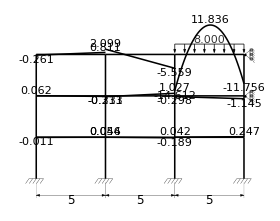
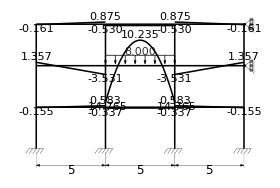
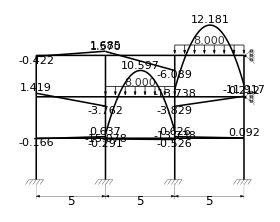

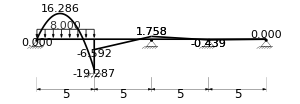

```mathematica
Graphics[ makeBuildingVerticalLoaded[ {3   }, {5, 5,5, 5  },
buildingBeamUniformLoadList -> {{1,1} -> 8 },
buildingBeamPointForceList -> {  },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { {1, 2} -> False, _ -> True },
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {1 -> None},
buildingSideSupportRightList -> {1 -> None },
buildingSupportList -> { },
buildingSolveColumnBeamDisplacementFunctions -> False,

buildingDimensionLabelHeightList -> None,
buildingShowBeamMoments -> True,
buildingFactorDisplacement -> 0.01,
buildingFactorMomentDiagrams -> 0.02,
buildingShowUndeformedDeformedList -> {True, False}

], ImageSize -> 300 ]
```

#### All members loaded

```mathematica
Row[ Table[Graphics[ makeBuildingVerticalLoaded[ {3, 3,3   }, {5, 5,5, 5, 5  },
buildingBeamUniformLoadList -> wn,
buildingBeamPointForceList -> {  },
buildingNodeMomentApplied -> {},
buildingColumnsInternalHingesList -> {_ -> Top},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {{_, _} -> 1},
buildingColumnOmitList -> { },
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {1 -> None},
buildingSideSupportRightList -> {1 -> None },
buildingSupportList -> {1 -> "fixed", 2 -> "fixed", 3 -> "fixed", 4 -> "fixed"},
buildingSolveColumnBeamDisplacementFunctions -> False,

buildingDimensionLabelHeightList -> None,
buildingShowBeamMoments -> True,
buildingFactorDisplacement -> 0.01,
buildingFactorMomentDiagrams -> 0.02,
buildingShowUndeformedDeformedList -> {True, False}

], ImageSize -> 300 ], {wn, { {_ -> 8} }}]
]
```

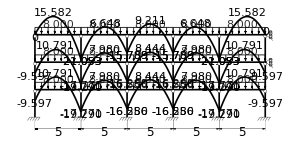

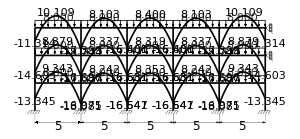

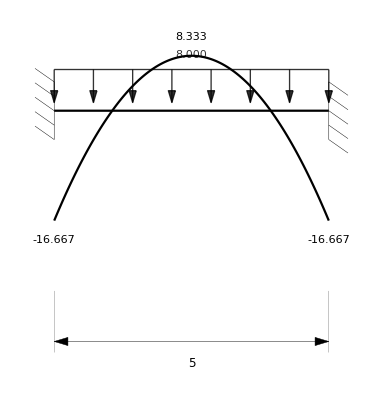

```mathematica
Graphics[ makeBuildingVerticalLoaded[ {3   }, {5  },
buildingBeamUniformLoadList -> { {1, 1} -> 8 },
buildingBeamPointForceList -> {  },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> {_ -> True },
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {1 -> "fixed"},
buildingSideSupportRightList -> {1 -> "fixed" },
buildingSupportList -> {1 -> "fixed", 2 -> "fixed", 3 -> "fixed", 4 -> "fixed"},
buildingSolveColumnBeamDisplacementFunctions -> False,

buildingDimensionLabelHeightList -> None,
buildingShowBeamMoments -> True,
buildingFactorDisplacement -> 0.01,
buildingFactorMomentDiagrams -> 0.02,
buildingShowUndeformedDeformedList -> {True, False}

]
]
```

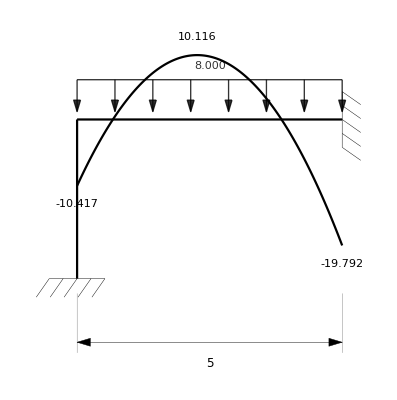

```mathematica
Graphics[ makeBuildingVerticalLoaded[ {3   }, {5  },
buildingBeamUniformLoadList -> { {1, 1} -> 8 },
buildingBeamPointForceList -> {  },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> {{1, 2} -> True },
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {1 -> None},
buildingSideSupportRightList -> {1 -> "fixed" },
buildingSupportList -> {1 -> "fixed", 2 -> "fixed", 3 -> "fixed", 4 -> "fixed"},
buildingSolveColumnBeamDisplacementFunctions -> False,

buildingDimensionLabelHeightList -> None,
buildingShowBeamMoments -> True,
buildingFactorDisplacement -> 0.01,
buildingFactorMomentDiagrams -> 0.02,
buildingShowUndeformedDeformedList -> {True, False}

]
]
```

#### Checkerboard members loaded

```mathematica
Row[ Table[Graphics[ makeBuildingVerticalLoaded[ {3, 3,3   }, {5, 5,5, 5, 5  },
buildingBeamUniformLoadList -> wn,
buildingBeamPointForceList -> {  },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { },
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {1 -> None},
buildingSideSupportRightList -> {1 -> None },
buildingSupportList -> {1 -> "fixed", 2 -> "fixed", 3 -> "fixed", 4 -> "fixed"},
buildingSolveColumnBeamDisplacementFunctions -> False,

buildingDimensionLabelHeightList -> None,
buildingShowBeamMoments -> True,
buildingFactorDisplacement -> 0.01,
buildingFactorMomentDiagrams -> 0.02,
buildingShowUndeformedDeformedList -> {True, False}

], ImageSize -> 500 ], {wn, { {{i_, j_} /; EvenQ[ i + j ] -> 8} }}]
]
```

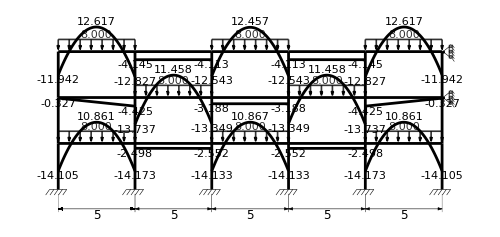

```mathematica
Graphics[ makeBuildingVerticalLoaded[ {3   }, {5, 5, 10  },
buildingBeamUniformLoadList -> { {1, 2} -> 8 },
buildingBeamPointForceList -> {  },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> {{1, 1} | {1, 4} -> True },
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {1 -> "fixed"},
buildingSideSupportRightList -> {1 -> "fixed" },
buildingSupportList -> {1 -> "fixed", 2 -> "fixed", 3 -> "fixed", 4 -> "fixed"},
buildingSolveColumnBeamDisplacementFunctions -> False,

buildingDimensionLabelHeightList -> None,
buildingShowBeamMoments -> True,
buildingFactorDisplacement -> 0.01,
buildingFactorMomentDiagrams -> 0.02,
buildingShowUndeformedDeformedList -> {True, False}

]
]
```

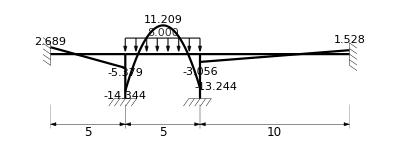

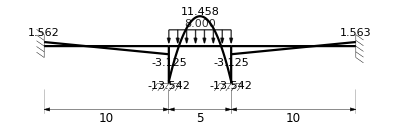

```mathematica
Graphics[ makeBuildingVerticalLoaded[ {3   }, {10, 5, 10  },
buildingBeamUniformLoadList -> { {1, 2} -> 8 },
buildingBeamPointForceList -> {  },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> {{1, 1} | {1, 4} -> True },
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {1 -> "fixed"},
buildingSideSupportRightList -> {1 -> "fixed" },
buildingSupportList -> {1 -> "fixed", 2 -> "fixed", 3 -> "fixed", 4 -> "fixed"},
buildingSolveColumnBeamDisplacementFunctions -> False,

buildingDimensionLabelHeightList -> None,
buildingShowBeamMoments -> True,
buildingFactorDisplacement -> 0.01,
buildingFactorMomentDiagrams -> 0.02,
buildingShowUndeformedDeformedList -> {True, False}

]
]
```

#### Competition on a beam

```mathematica
Manipulate[
Column[ {Graphics[ makeBuildingVerticalLoaded[ {0.1  }, {5, 5,5  },
buildingBeamUniformLoadList -> { {1, 2} -> w },
buildingBeamPointForceList -> {  },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { _ -> True },
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {},
buildingSideSupportRightList -> {1 -> "fixed" },
buildingSupportList -> {},
buildingSolveColumnBeamDisplacementFunctions -> False,

buildingDimensionLabelHeightList -> None,
buildingShowBeamMoments -> True,
buildingFactorDisplacement -> 0.01,
buildingFactorMomentDiagrams -> 0.15,
buildingShowUndeformedDeformedList -> {True, False}

], ImageSize -> 500 ],
Graphics[ makeBuildingVerticalLoaded[ {0.1  }, {5, 5,5  },
buildingBeamUniformLoadList -> {  },
buildingBeamPointForceList -> { {1, 3} -> {r, P} },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { _ -> True },
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {},
buildingSideSupportRightList -> {1 -> "fixed" },
buildingSupportList -> {},
buildingSolveColumnBeamDisplacementFunctions -> False,

buildingDimensionLabelHeightList -> None,
buildingShowBeamMoments -> True,
buildingFactorDisplacement -> 0.01,
buildingFactorMomentDiagrams -> 0.15,
buildingShowUndeformedDeformedList -> {True, False}

], ImageSize -> 500 ],
Graphics[ makeBuildingVerticalLoaded[ {0.1  }, {5, 5,5  },
buildingBeamUniformLoadList -> { {1, 2} -> w },
buildingBeamPointForceList -> { {1, 3} -> {r, P} },
buildingNodeMomentApplied -> {},
buildingBeamsEIMagnitudeList -> {_ -> 1},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingColumnOmitList -> { _ -> True },
buildingBeamOmitList -> {},
buildingSideSupportLeftList -> {},
buildingSideSupportRightList -> {1 -> "fixed" },
buildingSupportList -> {},
buildingSolveColumnBeamDisplacementFunctions -> False,

buildingDimensionLabelHeightList -> None,
buildingShowBeamMoments -> True,
buildingFactorDisplacement -> 0.01,
buildingFactorMomentDiagrams -> 0.15,
buildingShowUndeformedDeformedList -> {True, False}

], ImageSize -> 500 ]}],
{{P, 3, Dynamic[ Row[ {"P = ", P}]]}, 0, 10, 0.5},
{{r, 0.5, Dynamic[ Row[ {"r = ", 0.5}]]}, 0, 1, 0.1},
{{w, 1, Dynamic[ Row[ {"w = ", w}]]}, 0, 10, 0.5},
ControlPlacement -> Left
]
```

```mathematica
`
```

```mathematica
Interpolation[ { {0, 0.216}, {1, -0.865}}][ 0.5]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

-0.3245

```mathematica
Interpolation[ { {0, -1.44}, {1, 0.72}}][ 0.5]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

-0.36